```mathematica
originalLo = {1,1};
originalHi = {15,10};
frames = 1800;
Manipulate[
Graphics[
{
EdgeForm[Dashed],White,Rectangle[originalLo,originalHi],
Rectangle[originalLo+(lo-originalLo)Log[(ⅇ-1)t/frames+1],originalHi-(originalHi-hi)Log[(ⅇ-1)t/frames+1]]
}
],
{{t,0},0,frames},
{{lo,{5,5}},Locator},
{{hi,{9,7}},Locator}
]
```

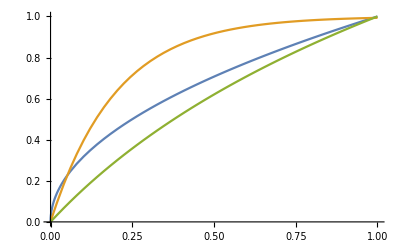

```mathematica
Plot[{√x,1-Exp[-5x],Log[(ⅇ-1)x+1]},{x,0,1}]
```